```mathematica
"Exercício 1";
MDC[a_,b_,c_]:=
Module[
{la={},lb={},lc={},in},
For[
i=1,
i<=Min[a,b,c],
i++,
If[Mod[a,i]==0,AppendTo[la,i]]
];
For[
i=1,
i<=Min[a,b,c],
i++,
If[Mod[b,i]==0,AppendTo[lb,i]]
];
For[
i=1,
i<=Min[a,b,c],
i++,
If[Mod[c,i]==0,AppendTo[lc,i]]
];
Part[Intersection[la,lb,lc],-1]
]

a=360;
b=180;
c=45;
MDC[a,b,c]
```

45

```mathematica
"Exercício 2";

g[a_]:=
Module[{l={}},
AppendTo[l,Part[a,1]];
AppendTo[l,Part[a,-1]];
Total[l]
]
v={1,2,3,4,5};
g[v]
```

6

```mathematica
"Exercício 3";
h[a_]:=
Module[
{lp=Table[Prime[i],{i,1,50000}],
lm=Table[2^i-1,{i,1,1000}],in,k},
in=Intersection[lp,lm];
k=Table[in[[i]],{i,a}]
]
h[4]
```

{3,7,31,127}

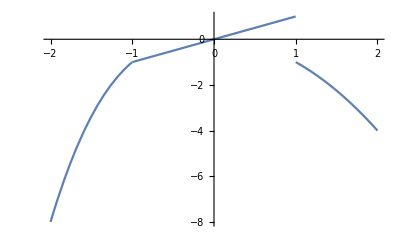

```mathematica
"Exercício 4";

Plot[Which[x≤-1,x^3,-1≤x≤ 1,x,x≥1,-x^2],{x,-2,2}]
```

```mathematica
"Exercício 5";
f2[n_]:=
Module[{l={}},
For[
i=1,
i≤n/2,
i++,
If[Mod[n,i]==0,AppendTo[l,i]]
];
l
]

IsItPerfect[n_]:=
If[n==Total[f2[n]],True,False];

PerfNumb[n_]:=
Module[{l={}},
For[
i=1,
i≤n,
i++,
If[IsItPerfect[i],AppendTo[l,i]]
];
l
]
```

{}

```mathematica
"Exercício 6";
Fac[n_]:=
If[Positive[n],Module[{a=1},
For[
j=1,
j≤n,
j++,
a*=j
];
a],Print["The function cannot be applied to a negative value"]
]
FacList[m_]:=
Module[{k={}},
For[
i=1,
Fac[i]<=m,
i++,
AppendTo[k,Fac[i]]
];
k
]
FacList[600]
```

{1,2,6,24,120}

```mathematica
"Exercício 7";
Divi[n_]:=
Module[{k={}},
For[
i=1,
i≤n,
i++,
If[Mod[n,i]==0,AppendTo[k,i]]
];
k
]
Divi[133]
```

{1,7,19,133}